```mathematica
SetDirectory[NotebookDirectory[]];
Clear[rh,rd,answer,rdlist,Blist];
rh=1;
L=2;
f=-((r-rh)*(r-rd)*(r+rd+rh))/((rh^2+rd*rh+rd^2)*r);
rdlist={10} ;(*{10,20,40,80, 160};*)
Blist={0,3,10};(*Range[0,10]; *)
x2list={40};(*{60,100,150,300,600};*)
```

```mathematica
kk=1;
While[kk≤Length[rdlist],
rd=rdlist[[kk]];
M=1/2*((rd^2 rh+rh^2 rd)/(rd^2+rd rh+rh^2));
kappa=1/(rd^2+rd rh+rh^2)^(1/2);
kh=D[f,r]/2/.r->rh;
kd=-D[f,r]/2/.r->rd;
vr1=f*(L*(L+1)/r^2-6*M/r^3);

rt=-(((rd^2+rd rh+rh^2) (rd (rd+2 rh) Log[r-rd]-rh (2 rd+rh) Log[r-rh]+(-rd^2+rh^2) Log[r+rd+rh]))/((rd-rh) (2 rd+rh) (rd+2 rh)));

r0=-10*rh;
sigma=rh;
rlist=Join[Table[N[rh+Exp[kh*ii/16]],{ii,-500,30}],Table[N[2.001+ii/10],{ii,0,10*(rd-3)}],Table[N[rd-Exp[-kd*ii]],{ii,-20,180}]];
rtlist=Table[N[Re[rt/.r->rlist[[ii]]]],{ii,1,Length[rlist]}];
(* Export["rtlist_rd"<>IntegerString[rd]<>".txt",rtlist]; *)

jj=1;
While[jj≤Length[Blist],
BB=3*Blist[[jj]];

vr1list=Table[N[vr1/.r->rlist[[ii]]],{ii,1,Length[rlist]}];
vr2list=Table[BB*kh^2*kappa^2*((f/.r->rlist[[ii]])*NIntegrate[Sqrt[1-f]/f,{r,2*rh,rlist[[ii]]}])^2,{ii,1,Length[rlist]}];
vrlist=vr1list+vr2list;

	vrrh=(vr1+BB*kh^2*kappa^2*(f*Integrate[Sqrt[1-(2*kh)*(r-rh)]/((2*kh)*(r-rh)),r])^2)-((vr1+BB*kh^2*kappa^2*(f*Integrate[Sqrt[1-(2*kh)*(r-rh)]/((2*kh)*(r-rh)),r])^2)/.r->rlist[[1]])+vrlist[[1]];(*near Subscript[r, H]*)
vrrd=(vr1+BB*kh^2*kappa^2*(f*Integrate[Sqrt[1-(2*kd)*(rd-r)]/((2*kd)*(rd-r)),r])^2)-((vr1+BB*kh^2*kappa^2*(f*Integrate[Sqrt[1-(2*kd)*(rd-r)]/((2*kd)*(rd-r)),r])^2)/.r->rlist[[Length[rlist]]])+vrlist[[Length[rlist]]];(*near Subscript[r, d]*)

dat2=Flatten/@Transpose[{rtlist,vrlist}];
(*Export["vrlist_rd"<>IntegerString[rd]<>"_B"<>IntegerString[BB/3]<>".txt",dat2,"Table"]; *)

x1=-20;
x2=x2list[[kk]];
ifun=Interpolation[Transpose@{rtlist,vrlist}];
(*vrrh/.r->rh+Exp[2*kh*(x-rtlist[[1]])]*(rlist[[1]]-rh)*)
ifunfull1[xx_]:=Piecewise[{{vrrh/.r->rh+Exp[2*kh*(xx-rtlist[[1]])]*(rlist[[1]]-rh),xx<=rtlist[[1]]&&xx≥-x1},{ifun[xx],xx>rtlist[[1]]&&xx<rtlist[[Length[rlist]]]},{vrrd/.r->rd-Exp[-2*kd*(xx-rtlist[[Length[rlist]]])]*(rd-rlist[[Length[rlist]]]),xx≥rtlist[[Length[rlist]]]&&xx≤x2}}];

ii=1;
wlist=0.01*Range[1,400];
CinR=wlist;
CinI=wlist;
PsiR=wlist;
PsiI=wlist;
Pow=wlist;
While[ii≤Length[wlist],
w=wlist[[ii]];

EQ=D[y[x],{x,2}]+(w^2-ifunfull1[x])*y[x];
BC=Exp[-I*w*x1];
BC1=-I*w*Exp[-I*w*x1];
sol=NDSolve[{EQ==0,y[x1]==BC,y'[x1]==BC1},y,{x,x1,x2},MaxSteps->10^6];

yinf=y[x2]/.sol[[1]];yinf1=y'[x2]/.sol[[1]];

yinfana=(Cin*Exp[-I*w*x2]+Cout*Exp[I*w*x2]);
yinfana1=(D[Cin*Exp[-I*w*x]+Cout*Exp[I*w*x],x])/.x->x2;
solcin=Solve[{yinf==yinfana,yinf1==yinfana1},{Cin,Cout}][[1]];
Aint=NIntegrate[Exp[-(x-r0)^2/sigma^2]*y[x]/.sol//Release,{x,x1,x2}(*,WorkingPrecision->8,PrecisionGoal->8,MaxRecursion->6*)][[1]];

CinR[[ii]]=Re[Cin/.solcin[[1]]];
CinI[[ii]]=Im[Cin/.solcin[[1]]];
Psi=Aint/(2*I*w*Cin)/.solcin[[1]];
PsiR[[ii]]=Re[Psi];
PsiI[[ii]]=Im[Psi];
Pow[[ii]]=w^2*Abs[Psi]^2;
(* answer[ii]={w,Cin/.solcin[[1]],Psi=Aint/(2*I*w*Cin)/.solcin[[1]],P=w^2*Abs[Psi]^2}; *)
ii++;];
(* Export["answer_rd"<>IntegerString[rd]<>"_"<>IntegerString[BB]<>".txt",Table[answer[ii],{ii,1,Length[wlist]}]];*)
dat1=Flatten/@Transpose[{wlist,CinR,CinI,PsiR,PsiI,Pow}];
Export["schrodinger_rd"<>IntegerString[rd]<>"_3D"<>IntegerString[BB/3]<>".txt",dat1,"Table"];


jj++;];
kk++;];
```

vrlist_rd40_B60.txt

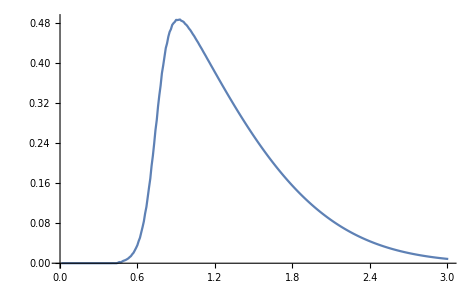

```mathematica
(*plot power spctrum @detector*)
Tabe=Table[answer[ii],{ii,0,Nmaxx}];
Tabeexport=Table[{N[Tabe[[i,1]]],Re[Tabe[[i,3]]],Im[Tabe[[i,3]]],Tabe[[i,4]]},{i,1,Length[Tabe]}];
Tabepower1=Table[{Tabe[[i,1]],Tabe[[i,4]]},{i,1,Length[Tabe]}];
ListPlot[Tabepower1,PlotRange->{All,All},Joined->True]
```

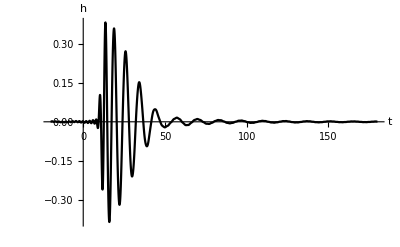

```mathematica
dat1=Table[{N[Tabe[[i,1]]],Re[Tabe[[i,3]]]+I*Im[Tabe[[i,3]]]},{i,1,Length[Tabe]}];
ff1=Sum[Re[dat1[[i,2]]*Exp[-I*dat1[[i,1]]*(t)]]*(dat1[[i+1,1]]-dat1[[i,1]]),{i,1,Length[dat1]-1}];
Plot[{ff1},{t,-20,180},PlotRange->All,AxesLabel->{"t","h"},LabelStyle->Directive[Medium,FontSize->16],PlotStyle->{Black}]
```

```mathematica
BB=0;
rlist=Join[Table[N[rh+Exp[kh*ii/16]],{ii,-500,30}],Table[N[2.001+ii/10],{ii,0,10*(rd-3)}],Table[N[rd-Exp[-kd*ii]],{ii,-20,180}]];
rtlist=Table[N[Re[rt/.r->rlist[[ii]]]],{ii,1,Length[rlist]}];
vr1list=Table[N[vr1/.r->rlist[[ii]]],{ii,1,Length[rlist]}];
vr2list=Table[BB*kh^2*kappa^2*((f/.r->rlist[[ii]])*NIntegrate[Sqrt[1-f]/f,{r,2*rh,rlist[[ii]]}])^2,{ii,1,Length[rlist]}];
vrlist=vr1list+vr2list;

vrrh=(vr1+BB*kh^2*kappa^2*(f*Integrate[Sqrt[1-(2*kh)*(r-rh)]/((2*kh)*(r-rh)),r])^2)-((vr1+BB*kh^2*kappa^2*(f*Integrate[Sqrt[1-(2*kh)*(r-rh)]/((2*kh)*(r-rh)),r])^2)/.r->rlist[[1]])+vrlist[[1]];(*near Subscript[r, H]*)
vrrd=(vr1+BB*kh^2*kappa^2*(f*Integrate[Sqrt[1-(2*kd)*(rd-r)]/((2*kd)*(rd-r)),r])^2)-((vr1+BB*kh^2*kappa^2*(f*Integrate[Sqrt[1-(2*kd)*(rd-r)]/((2*kd)*(rd-r)),r])^2)/.r->rlist[[Length[rlist]]])+vrlist[[Length[rlist]]];(*near Subscript[r, d]*)

ifun=Interpolation[Transpose@{rtlist,vrlist}];
```

```mathematica
x1=-20;x2=50;
(*vrrh/.r->rh+Exp[2*kh*(x-rtlist[[1]])]*(rlist[[1]]-rh)*)
ifunfull1[xx_]:=Piecewise[{{vrrh/.r->rh+Exp[2*kh*(xx-rtlist[[1]])]*(rlist[[1]]-rh),xx<=rtlist[[1]]&&xx≥-x1},{ifun[xx],xx>rtlist[[1]]&&xx<rtlist[[Length[rlist]]]},{vrrd/.r->rd-Exp[-2*kd*(xx-rtlist[[Length[rlist]]])]*(rd-rlist[[Length[rlist]]]),xx≥rtlist[[Length[rlist]]]&&xx≤x2}}];
```

```mathematica
ii=0;
Nmaxx=300;
While[ii<Nmaxx+1,
w=0.01+0.01*ii;

EQ=D[y[x],{x,2}]+(w^2-ifunfull1[x])*y[x];
BC=Exp[-I*w*x1];
BC1=-I*w*Exp[-I*w*x1];
sol=NDSolve[{EQ==0,y[x1]==BC,y'[x1]==BC1},y,{x,x1,x2},MaxSteps->10^6];

yinf=y[x2]/.sol[[1]];yinf1=y'[x2]/.sol[[1]];

yinfana=(Cin*Exp[-I*w*x2]+Cout*Exp[I*w*x2]);
yinfana1=(D[Cin*Exp[-I*w*x]+Cout*Exp[I*w*x],x])/.x->x2;
solcin=Solve[{yinf==yinfana,yinf1==yinfana1},{Cin,Cout}][[1]];
Aint=NIntegrate[Exp[-(x-r0)^2/sigma^2]*y[x]/.sol//Release,{x,x1,x2}(*,WorkingPrecision->8,PrecisionGoal->8,MaxRecursion->6*)][[1]];

answer[ii]={w,Cin/.solcin[[1]],Psi=Aint/(2*I*w*Cin)/.solcin[[1]],P=w^2*Abs[Psi]^2};
ii++;];

Export["answer_temp_B0.txt",Table[answer[ii],{ii,0,Nmaxx}]];
```

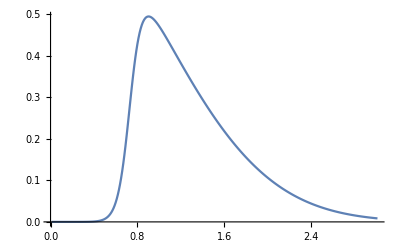

```mathematica
(*plot power spctrum @detector*)
Tabe=Table[answer[ii],{ii,0,Nmaxx}];
Tabeexport=Table[{N[Tabe[[i,1]]],Re[Tabe[[i,3]]],Im[Tabe[[i,3]]],Tabe[[i,4]]},{i,1,Length[Tabe]}];
Tabepower1=Table[{Tabe[[i,1]],Tabe[[i,4]]},{i,1,Length[Tabe]}];
ListPlot[Tabepower1,PlotRange->{All,All},Joined->True]
```

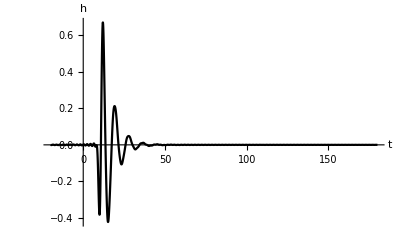

```mathematica
dat1=Table[{N[Tabe[[i,1]]],Re[Tabe[[i,3]]]+I*Im[Tabe[[i,3]]]},{i,1,Length[Tabe]}];
ff1=Sum[Re[dat1[[i,2]]*Exp[-I*dat1[[i,1]]*(t)]]*(dat1[[i+1,1]]-dat1[[i,1]]),{i,1,Length[dat1]-1}];
Plot[{ff1},{t,-20,180},PlotRange->All,AxesLabel->{"t","h"},LabelStyle->Directive[Medium,FontSize->16],PlotStyle->{Black}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
answer=Import["answer_temp_rd10_B0.txt",{"Table"}];
```

```mathematica
Nmaxx=Length[answer]-1
```

300

```mathematica
Tabe=Table[answer[ii],{ii,0,Nmaxx}];
```

```mathematica
Tabeexport=Table[{N[Tabe[[i,1]]],Re[Tabe[[i,3]]],Im[Tabe[[i,3]]],Tabe[[i,4]]},{i,1,Length[Tabe]}];
```

```mathematica
answer[[1,8]]
```

4.855031617125335*^-10}

```mathematica
Abs[1+2*I]
```

√5

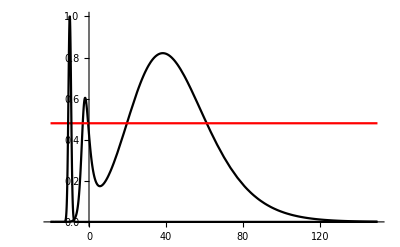
```mathematica
temp=ListPlot[{Transpose@{rtlist,vrlist}},Joined->False,PlotRange->{{x1,x2},All}];
temp1=Plot[{{ifunfull1[x],0.6928^2},Exp[-(x-r0)^2/sigma^2]},{x,x1,x2},PlotStyle->{Black,Red},PlotRange->{All,All}]
-Graphics-
```